Simulate a beamforming microphone array to determine effectiveness of spatial filtering in 2D and 3D space.
Rowan Sharman
Shell TechWorks
2018

```mathematica
(*---------------Pre-Evaluation---------------*)
vSound=34300;

(*Focus and mic coordinates in cm*)

(*focus={0,0,0};*)

(*focus={30,0,0};*)
focus={0,-9,-16};


micArray = {{17,-10,0},{7,-1,0}};
mirror=micArray;
mirror[[All,1]]=-1*micArray[[All,1]];
micArray=Union[micArray, mirror];


(*micArray={{-21,0,0},{-15,0,0},{-9,0,0},{-3,0,0},{3,0,0},{9,0,0},{15,0,0},{21,0,0}};*)
(*micArray={{-10,0,0},{-5,0,0},{-3,0,0},{-1,0,0},{0,0,0}};*)
(*micArray={{0,0,0},{10,0,0}};*)
(*micArray={{5,0,0}};*)



(*arrayRadius = 11;
arrayElements = 8;
arrayAngle = 150Degree;
startAngle = π/2 - arrayAngle/2 ;
angleStep =arrayAngle/(arrayElements-1);

micArray={};

For[i=1, i≤ arrayElements, i ++,
θ=startAngle+angleStep*(i-1);
x=arrayRadius * Cos[θ];
y=arrayRadius * Sin[θ];
z=0;
AppendTo[micArray,{x,y,z}];
];*)


getFocusDistances[focus_, mics_]:=
Module[{f=focus, m=mics},
distOffsets={};
For[j=1,j≤ Length[m],j++,
focusDeltas=m[[j]]-f;
distOffset = Sqrt[Total[focusDeltas^2]];
AppendTo[distOffsets, distOffset];
];
distOffsets
]

focusDistances2D=getFocusDistances[focus[[;;2]],micArray[[All,;;2]]];
focusDistances3D=getFocusDistances[focus,micArray];

mycf=Function[x,Blend[{White,Orange,Red, Black},x]];

(*ranges for plots*)
r={{-20,20},
{-20,20},
{-20,20}};

(*r={{-20,40},
{-30,30},
{-30,30}};*)

Print["Microphone Array:",MatrixForm[micArray]//N]
Print["2D Focus Distances:",MatrixForm[focusDistances2D]//N]
Print["3D Focus Distances:",MatrixForm[focusDistances3D]//N]



(*---------------Pre-Evaluation---------------*)
```

Microphone Array:(-17. | -10. | 0.
-7. | -1. | 0.
7. | -1. | 0.
17. | -10. | 0.)

2D Focus Distances:(17.0294
10.6301
10.6301
17.0294)

3D Focus Distances:(23.3666
19.2094
19.2094
23.3666)

```mathematica
(*---------------Heavy Evaluation---------------*)
testFreq=1000; (*Hz*)

getSum[func_,point_,offsets_,mics_]:=
Module[{f=func,p=point,o=offsets,m=mics},
intersects={};
For[i=1,i≤ Length[m],i++,
deltas=m[[i]]-p;
dist = Sqrt[Total[deltas^2]]-o[[i]];
AppendTo[intersects,f /. t->dist];
];
Total[intersects]
]

getMax[func_,point_,freq_,offsets_,mics_]:=
Module[{f=func,p=point,fr=freq,o=offsets,m=mics},
wavelength=vSound/fr;
MaxValue[getSum[f1/.wl->wavelength,p,o,m],t0]/Length[mics]
]


f1=Sin[t*((2*π)/wl)+t0];

pattern2D=DensityPlot[getMax[f1,{x,y},testFreq,focusDistances2D,micArray[[All,;;2]]],{x,r[[1,1]],r[[1,2]]},{y,r[[2,1]],r[[2,2]]}, PlotLegends->Automatic, ColorFunction->mycf,ColorFunctionScaling->False,PlotPoints->10];

Beep[]
(*This will take a long time to run...*)
pattern3D=DensityPlot3D[getMax[f1,{x,y,z},testFreq,focusDistances3D, micArray],{x,r[[1,1]],r[[1,2]]},{y,r[[2,1]],r[[2,2]]},{z,r[[3,1]],r[[3,2]]}, PlotLegends->Automatic, ColorFunction->mycf,ColorFunctionScaling->False,OpacityFunction->Function[f,(f)^2],OpacityFunctionScaling->False,PlotPoints->20];

Beep[]

(*---------------Heavy Evaluation---------------*)
```

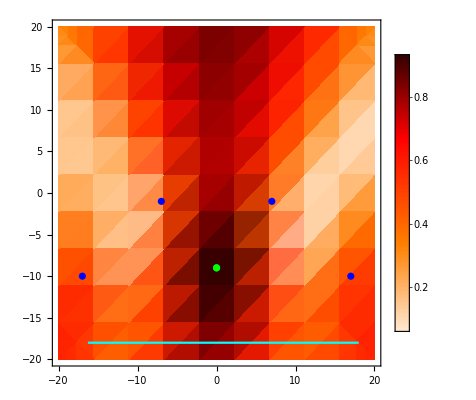

```mathematica
(*---------------Plotting---------------*)
micColor=Blue;
focusColor=Green;

wavelen=Plot[r[[2,1]]+2,{f,r[[1,2]]-2-(vSound/testFreq),r[[1,2]]-2},PlotStyle->Cyan];
(*This green bar at the bottom of the plot shows the actual wavelength compared to the array*)

mics2D = ListPlot[micArray[[All,;;2]], PlotStyle->micColor];
focusPoint2D=ListPlot[{focus[[;;2]]},PlotStyle->focusColor];
(*Note that 2D plot is not accurate for original array, it is accurate only for the flattened version of the array and the focus*)


mics3D = ListPointPlot3D[micArray,PlotRange->{r[[1]],r[[2]],r[[3]]} ,PlotStyle->micColor];
focusPoint3D=ListPointPlot3D[{focus},PlotRange->{r[[1]],r[[2]],r[[3]]},PlotStyle->focusColor];

Show[pattern2D, mics2D, focusPoint2D,wavelen]

(*This Manipulate allows you to slice the plot to see inside*)
Manipulate[
Show[{pattern3D, mics3D, focusPoint3D},ClipPlanes->{{x,y,z,d}}]
,{{x,-1},-1,1},{{y,0},-1,1},{{z,0},-1,1},{{d,3*r[[1,2]]},3*r[[1,1]],3*r[[1,2]]}]
(*---------------Plotting---------------*)
```